```mathematica
path1="/Volumes/Macintosh HD/Users/Yukun/Dropbox/Mudd/Spring 2015/E190Q/lab1/bin/x86/Release/semi_stable.csv";
path2="/Volumes/Macintosh HD/Users/Yukun/Dropbox/Mudd/Spring 2015/E190Q/lab1/bin/x86/Release/un_stable.csv";
path3="/Volumes/Macintosh HD/Users/Yukun/Dropbox/Mudd/Spring 2015/E190Q/lab1/bin/x86/Release/stable1.csv";
path4="/Volumes/Macintosh HD/Users/Yukun/Dropbox/Mudd/Spring 2015/E190Q/lab1/bin/x86/Release/stable2.csv";
```

```mathematica
plot[path_,kp_,color_]:=Module[{dataTable,timeAndDist},
dataTable=Import@path;
timeAndDist={#[[1]],#[[5]]/1000}&/@dataTable;

ListPlot[timeAndDist,
Joined->True,
PlotRange->{{0,Last[timeAndDist][[1]]},Automatic},
Axes->False,
Frame->True,
FrameLabel->{"Time [s]","Distance [m]"},
Epilog->{
Text["k_p = "<>ToString[kp],Scaled@{.85,.85}],
{color,PointSize@Medium,Point[timeAndDist]},
{Black,Dashed,Line[{{0,1000},{100,1000}}]}
},
PlotStyle->{color,Dashed},
BaseStyle->{FontFamily->"Times",FontSize-> 12},
LabelStyle->Black,
ImagePadding->{{50,50},{33,5}}
]
]
```

-Graphics-

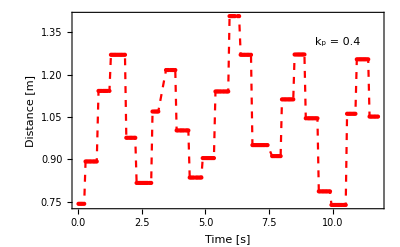

-Graphics-

-Graphics-

```mathematica
p1=plot[path1,0.15,Orange]
p2=plot[path2,0.4,Red]
p3=plot[path3,0.1,Darker@Green]
p4=plot[path4,0.1,Darker@Green]
```

```mathematica
Export[NotebookDirectory[]<>"figures/"<>"semi_stable.pdf",p1];
Export[NotebookDirectory[]<>"figures/"<>"unstable.pdf",p2];
Export[NotebookDirectory[]<>"figures/"<>"stable_close.pdf",p3];
Export[NotebookDirectory[]<>"figures/"<>"stable_far.pdf",p4];
```